## Mars Calendar

This is a note about the calendar on mars which has the following characteristics.

Starts from April 28, 1970

## Prep

```mathematica
Needs["Calendar`"]
```

```mathematica
m2e=1.027491252;
```

## Explanation

The idea is to coordinate the dates at 6th January 2000 on the Earth

## Coversion

In Mathematica, day difference can be easily calculated using DateDifference[]. However, we are just exploring an algrimth for our python or js program. The idea is to calculate Julian date.

The idea of the algrimth is to calculate the Julian dates and Mars sol dates. One of the key date is 6th January 2000 on the Earth when it was midnight at the Martian prime meridian.

### Dates away from coordinate date

The Seconds away from the coordinate date 6th January 2000 on the Earth is

```mathematica
dSec[date_]:=AbsoluteTime[date]-AbsoluteTime[{2000,1,6,24,0,0}]
```

Input date should have the format {y,m,d,h,m,s}

```mathematica
dSec[{2000,1,2,0,0,4}]
```

-431996

Number of dates on the earth away from the coordinate date

```mathematica
edDay[date_]:=dSec[date]/86400.0
```

Number of dates on Mars away from the coordinate date

```mathematica
mdDay[date_]:=edDay[date]/m2e
```

### Trace the calendar date on Mars

Mars use Darian calendar. The only thing we need to take care of is the leap year since leap year has 669 sol days while a common year has only 668 sol days on Mars.

Thus I would prefer to write a function that tells wether the year is a leap year or not in python. 

def is_leap_year(year):
    if year % 3000 == 0:
        return False
    elif year % 1000 == 0:
        return True
    elif year % 100 == 0:
        return False
    elif (year % 2 == 0) and (year % 10 == 0):
        return True
    else:
        return False
  
        
But here is a easier algrimth.

Define a step function which has a value of 1 for leap year but 0 for common year.

```mathematica
leapPlus[year_]:=If[Mod[year,3000]==0||Mod[year,3000]!=0&&Mod[year,1000]≠0&&Mod[year,100]==0||Mod[year,3000]!=0&&Mod[year,1000]≠0&&Mod[year,100]≠0&&Not[Mod[year,2]==0&&Mod[year,10]==0],0,1]
```

## Test this:

```mathematica
leapPlus[3000]
```

0

Next big deal is to know the coordinate date of Mars calendar in correspondence with Earth calendar.
Number of earth dates starting from 1970-04-28 to 2000-01-06

```mathematica
DateDifference[{1970,4,28},{2000,1,7}]
```

10846

Now we calculate the number of mars dates which should be very close to a integer.

```mathematica
10846/m2e
mS0=Floor[%]
0.8*m2e
```

10555.8

10555

0.821993

Calculate the how which calendar date on mars would correspond to so many Mars Sol dates

```mathematica
yearDayList[numerOfYears_]:=Table[668+leapPlus[i],{i,1,numerOfYears}]
```

{668,1336,2004,2672,3340,4008,4676,5344,6012,6681,7349,8017,8685,9353,10021,10689}

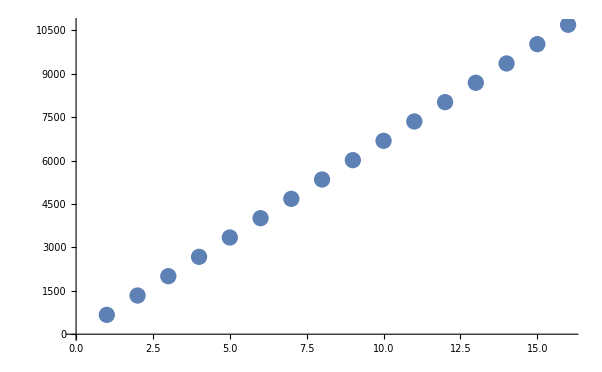

```mathematica
totalList=Table[Total@yearDayList[x],{x,1,16}]
ListPlot[totalList]
```

So we would have 15 years with extra 534 days. Now we are able to find the calendar date in Darian calendar of Mars. And we can determine that the  16th year is a common year.

```mathematica
10555-10021
leapPlus[16]
```

534

0

The Darian date of 2000-01-06 is the 19+1th month

```mathematica
Floor[534/28]
```

19

with the date

```mathematica
534-3*(5*28+27)-28
```

5

So we obtain the calendar date of 200-01-06 on Mars is Martian year 15, month 19, day 5, or 0015-19-05.

### Conversion Between the 2 calendar

Given a Earth calendar date, we first obtain the

```mathematica
24*60*60+39*60+35.244
%/(24*60*60)
```

88775.2

1.02749